# Week 11

## Sunday 26/5:

Adiabatic Theorem :

{{up[t]→InterpolatingFunction[{{-1000., 1000.}}, <>][t],down[t]→InterpolatingFunction[{{-1000., 1000.}}, <>][t]}}

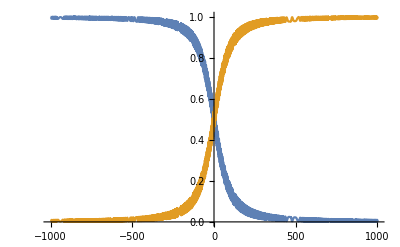

```mathematica
ham={{R t,Ω},{Ω,-R t}}; Ω=1; R=0.01;
vec={up[t],down[t]};
eq=Table[(ham.vec)[[i]]==I D[vec[[i]],t],{i,1,2}];
IC={up[-10/R]==1 , down[-10/R]==0};
sol=NDSolve[Join[eq,IC],vec,{t,-10/R,10/R}]
Plot[{Abs[up[t]/.sol]^2,Abs[down[t]/.sol]^2},{t,-10/R,10/R}]
```

Manipulate:

```mathematica
Quit[]
```

```mathematica
Ham={{δ,1},{1,-δ}}
```

{{δ,1},{1,-δ}}

```mathematica
reseg=Eigensystem[Ham];
res1=Normalize[reseg[[2,1]]];
res2=Normalize[reseg[[2,2]]];
Manipulate[{Show[Plot[reseg[[1]],{δ,-10,10}],Graphics[Locator[{δl,reseg[[1,e]]/.δ-> δl}]]],StringJoin[ToString[Normalize[reseg[[2,e]]][[1]]/.δ-> δl],"↓ ","+",ToString[Normalize[reseg[[2,e]]][[2]]/.δ-> δl],"↑"]},{δl,-10,10},{e,{1,2}}]
```

## Tuesday 28/5: